```mathematica
Clear["Global*`"]
```

## Training

Loading the segments comprising one full flight and concatenating

```mathematica
data=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-43-38_seg_1.csv"];
header=data⟦1,;;⟧;data1=data⟦2;;,;;⟧;
data2=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-43-38_seg_2.csv",HeaderLines->1];
data3=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-43-38_seg_3.csv",HeaderLines->1];
data4=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-43-38_seg_4.csv",HeaderLines->1];
dataFull=Join[data1,data2,data3,data4,1];
data=Join[data2,data3,1];
```

Plotting this data and animating the quad rotors position in the trajectory through time

```mathematica
Module[{pos,downSample},
pos=dataFull⟦;;,Position[header,#]⟦1,1⟧&/@{"pos x","pos y","pos z"}⟧;
downSample=Table[pos⟦n⟧,{n,1,Length[pos],20}];
Animate[
Show[
ListPointPlot3D[downSample,PlotTheme->"Detailed"]/.Point[a___]:>{Thick,Line[a]},
ListPointPlot3D[{pos⟦n⟧},PlotStyle->{Red,Large}]
],
{n,1,Length[pos],1,Appearance->"Labeled"},
AnimationRate->2000
]
]
```

We want to model the the force from each motor/rotor i, F_i.

(v^·)_B=1/m F_B-ω_B×v_B-Qᵀg
F_B=∑_(i∈{Motors}) F_i
F_B=m((v^·)_B+ω_B×v_B+Qᵀg)

The first method we use to do this is the modeling each each

x=(v_B ᵀ | ω_B ᵀ | Ωᵀ)ᵀ
^B F:ℝ^10→ℝ^3

Modeling this as a second order polynomial, we can write F_B using Einstein tensor notation as:

(F_B)_i=A_i+∑_(j=1)^(#x) B_(i,j)x_j+∑_(j=1)^Abs[x] ∑_(k=1)^Abs[x] C_(i,j,k)x_j x_k

Here A is a column vector (bias term), B is a matrix (linear term), C is a 3rd order tensor (quadratic term). Inorder to use linear algebra tools we can reorder this into a matrix problem as follows:

D=(A_(3x 1) | B_(3×Abs[x]) | (C_(i,j,1) | … | C_(i,j,Abs[x]))_(3×(Abs[x]·Abs[x]))), z=(𝟙
x
x⊗x)
F_B=D z ⟹ F_B ᵀ=zᵀDᵀ
D≡3×(1+Abs[x]+Abs[x]^2)

Where ⊗ denotes the Kronecker product and Abs[x]is the dimension of the vector x.

### Extracting Data

```mathematica
Squeeze[A_]:=ArrayReshape[A,Dimensions[A]~DeleteCases~1];
```

```mathematica
x=data⟦;;,Position[header,#]⟦1,1⟧&/@{"pos x","pos y","pos z"}⟧;
v̇=data⟦;;,Position[header,#]⟦1,1⟧&/@{"acc x","acc y","acc z"}⟧;
Ω=data⟦;;,Position[header,#]⟦1,1⟧&/@{"mot 1","mot 2","mot 3","mot 4"}⟧;Subscript[v, B]=data⟦;;,Position[header,#]⟦1,1⟧&/@{"vel x","vel y","vel z"}⟧;Subscript[ω, B]=data⟦;;,Position[header,#]⟦1,1⟧&/@{"ang vel x","ang vel y","ang vel z"}⟧;
q=data⟦;;,Position[header,#]⟦1,1⟧&/@{"quat w","quat x","quat y","quat z"}⟧;
```

Converting set of quaternions to a set of Rotation matrices

```mathematica
ℛ=2({{(#⟦1⟧)^2+(#⟦2⟧)^2-1/2, #⟦2⟧#⟦3⟧-#⟦1⟧#⟦4⟧, #⟦2⟧#⟦4⟧+#⟦1⟧#⟦3⟧}, {#⟦2⟧#⟦3⟧+#⟦1⟧#⟦4⟧, (#⟦1⟧)^2+(#⟦3⟧)^2-1/2, #⟦3⟧#⟦4⟧-#⟦1⟧#⟦2⟧}, {#⟦2⟧#⟦4⟧-#⟦1⟧#⟦3⟧, #⟦3⟧#⟦4⟧+#⟦1⟧#⟦2⟧, (#⟦1⟧)^2+(#⟦4⟧)^2-1/2}})&/@q;
```

### Examining The Data

Plotting the body’s position and acceleration over the flight (excluding the takeoff and landing).

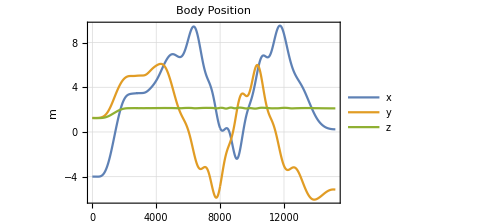
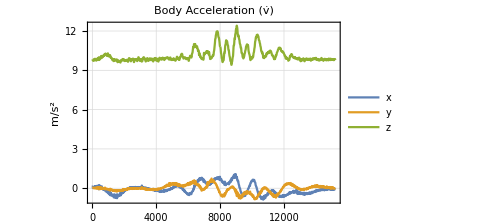
-Graphics- | -Graphics-

```mathematica
{{ListPlot[xᵀ,PlotTheme->"Detailed",Joined->True,PlotLabel->"Body Position",PlotLegends->{"x","y","z"},PlotRange->All,ImageSize->Medium,FrameLabel->{None,"m"}],
ListPlot[v̇ ᵀ,PlotTheme->"Detailed",Joined->True,PlotLabel->"Body Acceleration (v̇)",PlotLegends->{"x","y","z"},PlotRange->All,ImageSize->Medium,FrameLabel->{None,"m/s^2"}]}}//TableForm
```

From this we see that when the quad rotors body is stationary the recorded acceleration of the body is ~10m/s^2. Thus we note that the data labeled “acceleration body x”, “acceleration body y”, “acceleration body z” is actually a filtered fusion Vicon/IMU measurement. Thus we can modify our force fitting function:

F_B=m((v^·)_imu+ω_B×v_B)

Removing Coriolis from acceleration each time step:

```mathematica
ŷ=v̇+MapThread[#1×#2&,{Subscript[ω, B],Subscript[v, B]}];
```

Here ŷ is the net forces applied on the quad rotor by the quad rotor as well as the aerodynamic forces on the quad rotor.

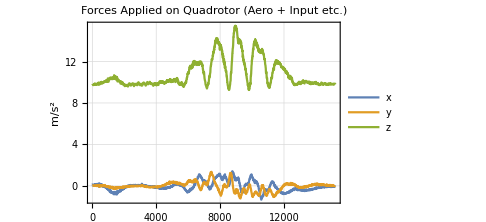

```mathematica
ListPlot[ŷ ᵀ,PlotTheme->"Detailed",
Joined->True,PlotLabel->"Forces Applied on Quadrotor (Aero + Input etc.)",
PlotLegends->{"x","y","z"},PlotRange->All,
ImageSize->Medium,FrameLabel->{None,"m/s^2"}]
```

Here we plot the motor speeds

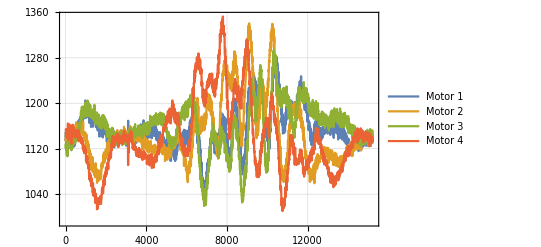

```mathematica
ListPlot[Ωᵀ,PlotTheme->"Detailed",Joined->True,PlotLegends->{"Motor 1","Motor 2","Motor 3","Motor 4"}]
```

### Fitting Model

As above we assume the forces on the quad rotor are a function of only the body linear and angular velocity, as well as the motor speeds.

x=(v_B ᵀ | ω_B ᵀ | Ωᵀ)ᵀ
F_B[x]:ℝ^10→ℝ^3

As  F_B is modeled as a quadratic we must apply the transform z=𝒻(x)=(𝟙
x
x⊗x). Constructing the set of sample points.

```mathematica
x̂=Join[Subscript[v, B],Subscript[ω, B],Ω,2];
X=Table[{Slot[i]},{i,Dimensions[x̂]⟦2⟧}];
𝒻=Evaluate[Squeeze[Join[{{1}},X,KroneckerProduct[X,X]]]]&;
ẑ=MapThread[𝒻,x̂ ᵀ];
```

Finally we can now compute the matrix D

```mathematica
𝔻=Module[{n},
n=10;
(PseudoInverse[ẑ⟦;;;;n⟧].ŷ⟦;;;;n⟧)ᵀ
];
```

```mathematica
𝔻.ẑ ᵀ//Dimensions
```

{{0.064871544297,0.064448941849,0.063780373037,0.063281047493,15208,0.01512077434,0.01670131928,0.01787592373,0.01797339136},{1},{1}}
 |  |  |  |

## Training Data

Loading in the training data

```mathematica
Squeeze[A_]:=ArrayReshape[A,Dimensions[A]~DeleteCases~1];
data=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-43-38_seg_2.csv"];
header=data⟦1,;;⟧;
data=data⟦2;;,;;⟧;
ListPointPlot3D[data⟦;;,Position[header,#]⟦1,1⟧&/@{"pos x","pos y","pos z"}⟧,PlotTheme->"Detailed"]
```

-Graphics3D-

We want to model the the force from each motor/rotor i, F_i.

(v^·)_B=1/m F_B-ω_B×v_B-Qᵀg
F_B=∑_(i∈{Motors}) F_i

The first method we use to do this is the modeling each each

x=(v_B ᵀ | ω_B ᵀ | Ωᵀ)ᵀ
F_B=Ω_i

Extract linear acceleration terms

```mathematica
v̇=data⟦;;,Position[header,#]⟦1,1⟧&/@{"acc x","acc y","acc z"}⟧;
Ω=data⟦;;,Position[header,#]⟦1,1⟧&/@{"mot 1","mot 2","mot 3","mot 4"}⟧;Subscript[v, B]=data⟦;;,Position[header,#]⟦1,1⟧&/@{"vel x","vel y","vel z"}⟧;Subscript[ω, B]=data⟦;;,Position[header,#]⟦1,1⟧&/@{"ang vel x","ang vel y","ang vel z"}⟧;
q=data⟦;;,Position[header,#]⟦1,1⟧&/@{"quat w","quat x","quat y","quat z"}⟧;
```

Converting set of quaternions to a set of Rotation matrices

```mathematica
ℛ=2({{(#⟦1⟧)^2+(#⟦2⟧)^2-1/2, #⟦2⟧#⟦3⟧-#⟦1⟧#⟦4⟧, #⟦2⟧#⟦4⟧+#⟦1⟧#⟦3⟧}, {#⟦2⟧#⟦3⟧+#⟦1⟧#⟦4⟧, (#⟦1⟧)^2+(#⟦3⟧)^2-1/2, #⟦3⟧#⟦4⟧-#⟦1⟧#⟦2⟧}, {#⟦2⟧#⟦4⟧-#⟦1⟧#⟦3⟧, #⟦3⟧#⟦4⟧+#⟦1⟧#⟦2⟧, (#⟦1⟧)^2+(#⟦4⟧)^2-1/2}})&/@q;
```

Remove Coriolis and gravity terms

```mathematica
g=({{0, 0, -9.81}})ᵀ;
ŷ=v̇+MapThread[#1×#2&,{Subscript[ω, B],Subscript[v, B]}]+Map[Flatten[#1ᵀ.g]&,ℛ];
x̂=Join[Subscript[v, B],Subscript[ω, B],Ω,2];
```

### Fitting

```mathematica
X=Table[{Slot[i]},{i,Dimensions[x̂]⟦2⟧}];
𝒻=Evaluate[Squeeze[Join[{{1}},X,KroneckerProduct[X,X]]]]&;
```

```mathematica
𝕂=PseudoInverse[MapThread[𝒻,x̂ ᵀ]].ŷ;
```

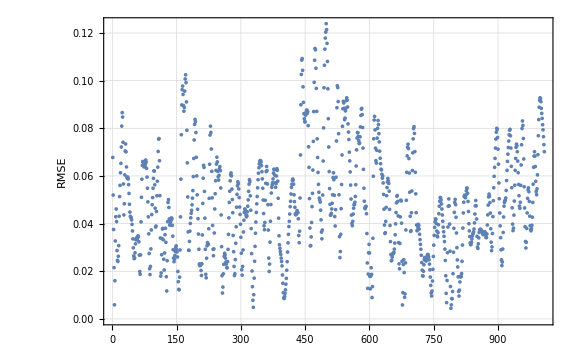

```mathematica
ListPlot[RootMeanSquare/@(MapThread[𝒻,x̂ ᵀ].𝕂-ŷ),PlotTheme->"Detailed",ImageSize->Large,FrameLabel->{None,"RMSE"}]
```

## Testing Data

```mathematica
Squeeze[A_]:=ArrayReshape[A,Dimensions[A]~DeleteCases~1];
data=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-43-38_seg_4.csv",HeaderLines->1];
(*header=data⟦1,;;⟧;
data=data⟦2;;,;;⟧;*)
ListPointPlot3D[data⟦;;,Position[header,#]⟦1,1⟧&/@{"pos x","pos y","pos z"}⟧,PlotTheme->"Detailed"]
```

-Graphics3D-

```mathematica
v̇=data⟦;;,Position[header,#]⟦1,1⟧&/@{"acc x","acc y","acc z"}⟧;
Ω=data⟦;;,Position[header,#]⟦1,1⟧&/@{"mot 1","mot 2","mot 3","mot 4"}⟧;Subscript[v, B]=data⟦;;,Position[header,#]⟦1,1⟧&/@{"vel x","vel y","vel z"}⟧;Subscript[ω, B]=data⟦;;,Position[header,#]⟦1,1⟧&/@{"ang vel x","ang vel y","ang vel z"}⟧;
q=data⟦;;,Position[header,#]⟦1,1⟧&/@{"quat w","quat x","quat y","quat z"}⟧;
```

```mathematica
ℛ=2({{(#⟦1⟧)^2+(#⟦2⟧)^2-1/2, #⟦2⟧#⟦3⟧-#⟦1⟧#⟦4⟧, #⟦2⟧#⟦4⟧+#⟦1⟧#⟦3⟧}, {#⟦2⟧#⟦3⟧+#⟦1⟧#⟦4⟧, (#⟦1⟧)^2+(#⟦3⟧)^2-1/2, #⟦3⟧#⟦4⟧-#⟦1⟧#⟦2⟧}, {#⟦2⟧#⟦4⟧-#⟦1⟧#⟦3⟧, #⟦3⟧#⟦4⟧+#⟦1⟧#⟦2⟧, (#⟦1⟧)^2+(#⟦4⟧)^2-1/2}})&/@q;
```

Remove Coriolis and gravity terms

```mathematica
g=({{0, 0, -9.81}})ᵀ;
ȳ=v̇+MapThread[#1×#2&,{Subscript[ω, B],Subscript[v, B]}]-Map[Flatten[#1ᵀ.g]&,ℛ];
(*x̂=Join[Subscript[v, B],Subscript[ω, B],Ω,2];*)
x̄=Join[Subscript[v, B],Ω,2];
```

```mathematica
X=Table[{Slot[i]},{i,Dimensions[x̄]⟦2⟧}];
𝒻=Evaluate[Squeeze[Join[{{1}},X,KroneckerProduct[X,X]]]]&;
```

```mathematica
𝕂1=PseudoInverse[MapThread[𝒻,x̄ ᵀ]].ȳ;
```

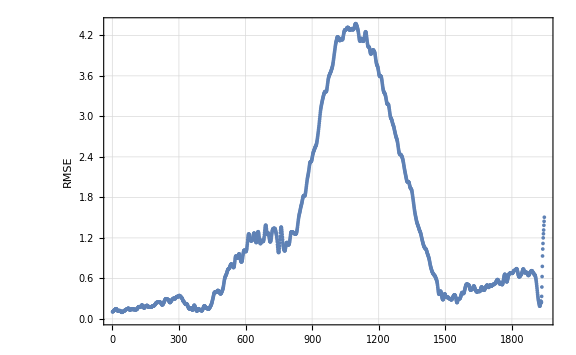

```mathematica
ListPlot[RootMeanSquare/@(MapThread[𝒻,x̄ ᵀ].𝕂-ȳ),PlotTheme->"Detailed",ImageSize->Large,FrameLabel->{None,"RMSE"}]
```

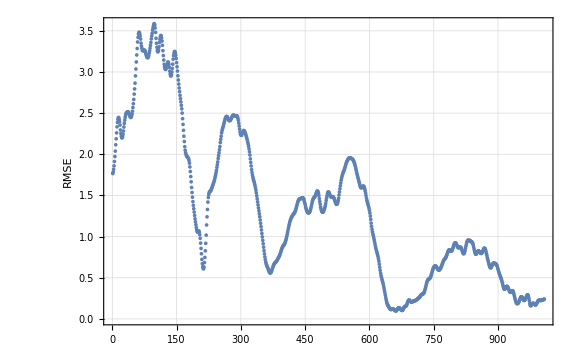

```mathematica
ListPlot[RootMeanSquare/@(MapThread[𝒻,x̂ ᵀ].𝕂1-ŷ),PlotTheme->"Detailed",ImageSize->Large,FrameLabel->{None,"RMSE"}]
```